# Solutions of Mathematica based Questions for Assignment 2, MATH7501, Sem 1, 2021

### Question 1iii

```mathematica
Sum[1/k^2,{k,1,∞}]
```

π^2/6

### Question 1iv

```mathematica
P[n_]:=Total[Table[N[1/k],{k,1,n}]]
```

```mathematica
Log[E]
```

1

```mathematica
diffSequence=Table[P[n]-Log[n],{n,1,1000}];
```

```mathematica
γApprox=Last[diffSequence]
```

0.577716

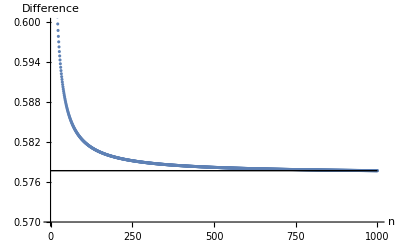

```mathematica
ListPlot[diffSequence,AxesOrigin->{0,0.57},PlotRange->{0.57,0.6},AxesLabel->{"n","Difference"},Epilog->{Line[{{0,γApprox},{1000,γApprox}}]}]
```

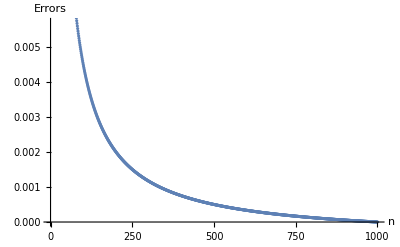

```mathematica
errors = diffSequence - γApprox;
ListPlot[errors,AxesLabel->{"n","Errors"}]
```

### Question 1vi

```mathematica
Module[{},
n=10;
data=Table[RandomReal[],{n}]

]
```

{0.614405,0.121693,0.0164655,0.866571,0.980211,0.369698,0.422367,0.308614,0.893082,0.944189}

```mathematica
?For
```

```mathematica
doIt[n_]:=(
For[
(*start*)
data=Table[RandomReal[],{n}];
m = -∞;
L=0;
i=1;
,
(*test*)
i≤n
,
(*incr*)
i=i+1;
,
(*body*)
If[data[[i]]> m,
m=data[[i]];
L=L+1;
];
;
];
N[L])
```

```mathematica
statEst[n_]:=Mean[Table[doIt[n],{10000}]]
```

```mathematica
est[n]:=Log[n]+γApprox
```

```mathematica
Print["n \t Difference"]
Table[{n,est[n]-statEst[n]},{n,1,10}] //TableForm
```

n 	 Difference

1 | 0.
2 | -0.0025
3 | 0.
4 | -0.0002
5 | -0.0009
6 | 0.0101
7 | -0.0007
8 | -0.0022
9 | 0.017
10 | -0.0042

### Question 5iii

```mathematica
f[x_]:=E^(-x^2/2)
taylorF[x_,K_]:=Sum[(D[f[x],{x,k}]/.x->0)x^k/(k!),{k,0,K}]
```

```mathematica
taylorFs = Table[taylorF[x,K],{K,1,20}];
taylorFs //TableForm
```

1
1-x^2/2
1-x^2/2
1-x^2/2+x^4/8
1-x^2/2+x^4/8
1-x^2/2+x^4/8-x^6/48
1-x^2/2+x^4/8-x^6/48
1-x^2/2+x^4/8-x^6/48+x^8/384
1-x^2/2+x^4/8-x^6/48+x^8/384
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120+x^16/10321920
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120+x^16/10321920
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120+x^16/10321920-x^18/185794560
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120+x^16/10321920-x^18/185794560
1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+x^12/46080-x^14/645120+x^16/10321920-x^18/185794560+x^20/3715891200

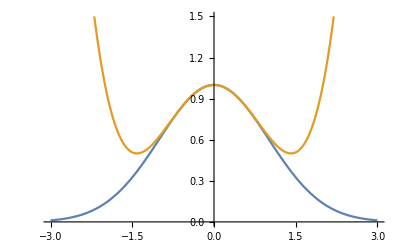

```mathematica
Plot[{f[x],taylorFs[[5]]},{x,-3,3},PlotRange->{0,1.5}]
```

```mathematica
maxError[a_,K_]:=Max[Table[Abs[f[x]-taylorFs[[K]]],{x,-a,a,0.1}]]
```

```mathematica
Table[maxError[0.5,K],{K,1,6}]//TableForm
```

0.117503
0.0074969
0.0074969
0.000315597
0.000315597
9.92342×10^-6

```mathematica
(*So we see that for a=0.5, K=6*)
```

```mathematica
Table[maxError[1.0,K],{K,1,10}]//TableForm
```

0.393469
0.106531
0.106531
0.0184693
0.0184693
0.00236399
0.00236399
0.000240174
0.000240174
0.000020243

```mathematica
(*So we see that for a=1.0, K=10*)
```

```mathematica
Table[maxError[1.5,K],{K,1,14}]//TableForm
```

0.675348
0.449652
0.449652
0.18316
0.18316
0.0541447
0.0541447
0.0125973
0.0125973
0.00241965
0.00241965
0.000396027
0.000396027
0.0000564923

```mathematica
(*So we see that for a=1.5, K=14*)
```

### Question 5iv

```mathematica
H[n_]:=Expand[Simplify[(-1)^n E^(x^2/2)D[E^(-x^2/2),{x,n}]]]
```

```mathematica
Table[H[n],{n,0,12}] //TableForm
```

1
x
-1+x^2
-3 x+x^3
3-6 x^2+x^4
15 x-10 x^3+x^5
-15+45 x^2-15 x^4+x^6
-105 x+105 x^3-21 x^5+x^7
105-420 x^2+210 x^4-28 x^6+x^8
945 x-1260 x^3+378 x^5-36 x^7+x^9
-945+4725 x^2-3150 x^4+630 x^6-45 x^8+x^10
-10395 x+17325 x^3-6930 x^5+990 x^7-55 x^9+x^11
10395-62370 x^2+51975 x^4-13860 x^6+1485 x^8-66 x^10+x^12

### Question 6iii

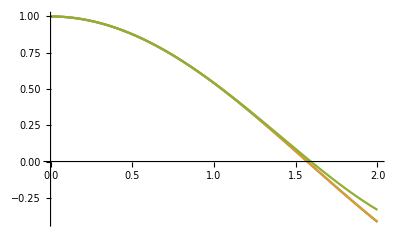

```mathematica
CosTaylor4[x_]:=1-x^2/2+x^4/(4!)
CosTaylor10[x_]:=1-x^2/2+x^4/(4!)-x^6/(6!)+x^8/(8!)-x^10/(10!)
Plot[{Cos[x],CosTaylor10[x],CosTaylor4[x]},{x,0,2}]
```

```mathematica
(*We see the 10'th order Taylro approximation is very close to the actual function. For illustration - also plotting the 4'th order approximation*)
Cos[1.5]-CosTaylor10[1.5]
```

2.67551×10^-7

```mathematica
numBisections=20;
a=0.0;
b=2.0;
bisectionTrace=Table[
mid = (a+b)/2;
If[CosTaylor10[mid]>0,a=mid,b=mid];
{a,b},
{numBisections}]
```

{{1.,2.},{1.5,2.},{1.5,1.75},{1.5,1.625},{1.5625,1.625},{1.5625,1.59375},{1.5625,1.57813},{1.57031,1.57813},{1.57031,1.57422},{1.57031,1.57227},{1.57031,1.57129},{1.57031,1.5708},{1.57056,1.5708},{1.57068,1.5708},{1.57074,1.5708},{1.57077,1.5708},{1.57079,1.5708},{1.57079,1.5708},{1.57079,1.5708},{1.5708,1.5708}}

```mathematica
(*Final error*)
Last[bisectionTrace][[1]]-Last[bisectionTrace][[2]]
```

-1.90735×10^-6

```mathematica
p=(Last[bisectionTrace][[1]]+Last[bisectionTrace][[2]])/2
```

1.5708

```mathematica
N[π/2]
```

1.5708